# (2) Electromagnetic perturbations

## Reference: E. Berti’s Black Hole Perturbation Theory Notes (ICTS) [https://www.icts.res.in/event/page/3071] Equation numbers cited throughout this document follow the numbering convention used in these notes to facilitate cross-referencing.

## (0) Set-up

```mathematica
SetDirectory["C:\Program Files\Wolfram Research\Mathematica\12.1\AddOns\Applications\xAct_1.2.0"];
```

```mathematica
<<xAct`xPert`(*perturbation theory*)
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

```mathematica
<<xAct`xCoba`(*tensor component calculations*)
```

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
<<MaTeX` ;(*LaTeX integration in text and output cells*)
```

```mathematica
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
SetOptions[MaTeX,FontSize->14];
```

```mathematica
mt = MaTeX;
```

Syntax to generate MaTeX formatted numbered equations:  “<expression>  \qquad   <equation_number> “ // mt
Execute the above in an input cell, and then paste result in a text cell.

```mathematica
$DefInfoQ=False;  (*turns off optional xAct messages*)
```

## (I) Definitions

```mathematica
DefManifold[M,4,IndexRange[a,f]]
```

```mathematica
DefMetric[-1,g[-a,-b],CD]
```

```mathematica
DefChart[B,M,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

Define the electromagnetic potential, A_a

```mathematica
DefTensor[A[-a],M];
```

Define the field tensor, F_ab

```mathematica
DefTensor[F[-a,-b],M, Antisymmetric[{1,2}]]
```

```mathematica
FtoArule= MakeRule[{F[-a,-b], CD[-a]@A[-b] -CD[-b]@A[-a] },MetricOn->All,ContractMetrics->True];
```

```mathematica
AtoFrule= MakeRule[{CD[-a]@A[-b],F[-a,-b]+CD[-b]@A[-a] },MetricOn->All,ContractMetrics->True];
```

Define metric perturbation

```mathematica
DefMetricPerturbation[g,h,ϵ]
```

Define vector field perturbation

```mathematica
DefTensorPerturbation[delA[LI[1],-a],A[-a],{M},PrintAs->"δA"]
```

Notational clean-up

```mathematica
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[K]^="F";
PrintAs[EinsteinCD]^="G";
$CovDFormat="Prefix";
PrintAs[Detg]^= "g";
```

## (III) The energy-momentum tensor and the Klein-Gordon equation

The Maxwell action is:

```mathematica
L=Sqrt[-Detg[]](1/4)(F[-a,-b]F[a,b])
```

1/4 √-g F |   |  
a | b F | a | b
  |

```mathematica
LwrtA = L/.FtoArule//ToCanonical
```

-1/2 √-g (▽_a A |  
b) (▽^b A | a
 )+1/2 √-g (▽_b A |  
a) (▽^b A | a
 )

First order variation in L

```mathematica
Lpert=LwrtA//Perturbation
```

1/2 (-√-g △[▽^b A | a
 ] (▽_a A |  
b)-√-g △[▽_a A |  
b] (▽^b A | a
 )+(△[g] (▽_a A |  
b) (▽^b A | a
 ))/(2 √-g))+1/2 (√-g △[▽^b A | a
 ] (▽_b A |  
a)+√-g △[▽_b A |  
a] (▽^b A | a
 )-(△[g] (▽_b A |  
a) (▽^b A | a
 ))/(2 √-g))

Variation in L expanded out in terms of the variation in our fundamental dynamical variables i.e. the metric, and the vector field

```mathematica
LpertExpanded = Lpert//ExpandPerturbation//Expand
```

-1/4 √-g h | 1 |   | c
  | c |   (▽_a A |  
b) (▽^b A | a
 )-1/2 √-g (▽_a δA | 1 |  
  | b) (▽^b A | a
 )+1/4 √-g h | 1 |   | c
  | c |   (▽_b A |  
a) (▽^b A | a
 )+1/2 √-g (▽_b δA | 1 |  
  | a) (▽^b A | a
 )+1/4 A |  
e √-g g | a | c
  |   g | b | d
  |   (▽_a A |  
b) (▽_c h | 1 | e |  
  |   | d)-1/4 A |  
e √-g g | a | c
  |   g | b | d
  |   (▽_b A |  
a) (▽_c h | 1 | e |  
  |   | d)-1/4 A |  
c √-g (▽^b A | a
 ) (▽^c h | 1 |   |  
  | a | b)+1/4 A |  
c √-g (▽^b A | a
 ) (▽^c h | 1 |   |  
  | b | a)+1/2 √-g g | b | d
  |   h | 1 | a | c
  |   |   (▽_a A |  
b) (▽_d A |  
c)+1/2 √-g g | a | c
  |   h | 1 | b | d
  |   |   (▽_a A |  
b) (▽_d A |  
c)-1/2 √-g g | b | d
  |   h | 1 | a | c
  |   |   (▽_b A |  
a) (▽_d A |  
c)-1/2 √-g g | a | c
  |   h | 1 | b | d
  |   |   (▽_b A |  
a) (▽_d A |  
c)-1/2 √-g g | a | c
  |   g | b | d
  |   (▽_a A |  
b) (▽_d δA | 1 |  
  | c)+1/2 √-g g | a | c
  |   g | b | d
  |   (▽_b A |  
a) (▽_d δA | 1 |  
  | c)+1/4 A |  
e √-g g | a | c
  |   g | b | d
  |   (▽_a A |  
b) (▽_d h | 1 | e |  
  |   | c)-1/4 A |  
e √-g g | a | c
  |   g | b | d
  |   (▽_b A |  
a) (▽_d h | 1 | e |  
  |   | c)-1/4 A |  
e √-g g | a | c
  |   g | b | d
  |   (▽_a A |  
b) (▽^e h | 1 |   |  
  | d | c)+1/4 A |  
e √-g g | a | c
  |   g | b | d
  |   (▽_b A |  
a) (▽^e h | 1 |   |  
  | d | c)

#### Energy-momentum tensor

```mathematica
tempMet1 =LpertExpanded//VarD[h[LI[1],a,b],CD]
```

-1/2 δ |   | 1
1 |   √-g g | c | d
  |   (▽_a A |  
c) (▽_b A |  
d)+1/2 δ |   | 1
1 |   √-g g | c | d
  |   (▽_b A |  
d) (▽_c A |  
a)+1/2 δ |   | 1
1 |   √-g g | c | d
  |   (▽_a A |  
d) (▽_c A |  
b)-1/2 δ |   | 1
1 |   √-g g | c | d
  |   (▽_c A |  
a) (▽_d A |  
b)-1/4 δ |   | 1
1 |   √-g g |   |  
a | b (▽_c A |  
d) (▽^d A | c
 )+1/4 δ |   | 1
1 |   √-g g |   |  
a | b (▽_d A |  
c) (▽^d A | c
 )

Substituting the value of the Kronecker delta component, δ |   | 1
1 |   = 1

```mathematica
tempMet2 = tempMet1/.delta[-LI[1],LI[1]]->1;
```

Since field equations are derived by imposing that the variation in action is zero, we can simplify our expression by multiplying with factor of 1/Sqrt[-Detg[]]

```mathematica
equationMetric = (-2/Sqrt[-Detg[]])tempMet2//Expand//ToCanonical//ContractMetric
```

(▽_a A |  
c) (▽_b A | c
 )-(▽_b A |  
c) (▽^c A |  
a)+(▽_c A |  
b) (▽^c A |  
a)-(▽_a A |  
c) (▽^c A |  
b)+1/2 g |   |  
a | b (▽_c A |  
d) (▽^d A | c
 )-1/2 g |   |  
a | b (▽_d A |  
c) (▽^d A | c
 )

```mathematica
temp=equationMetric//ScreenDollarIndices
```

(▽_a A |  
c) (▽_b A | c
 )-(▽_b A |  
c) (▽^c A |  
a)+(▽_c A |  
b) (▽^c A |  
a)-(▽_a A |  
c) (▽^c A |  
b)+1/2 g |   |  
a | b (▽_c A |  
d) (▽^d A | c
 )-1/2 g |   |  
a | b (▽_d A |  
c) (▽^d A | c
 )

```mathematica
temp/.{CD[-c][A[-d]]->F[-c,-d]+CD[-d][A[-c]]}//ToCanonical
```

(▽_a A | c
 ) (▽_b A |  
c)-(▽_b A |  
c) (▽^c A |  
a)+(▽_c A |  
b) (▽^c A |  
a)-(▽_a A |  
c) (▽^c A |  
b)+1/2 F |   |  
c | d g |   |  
a | b (▽^d A | c
 )

```mathematica
%/.{CD[-b][A[-c]]->F[-b,-c]+CD[-c][A[-b]]}//ToCanonical
```

F |   |  
b | c (▽_a A | c
 )-F |   |  
b | c (▽^c A |  
a)+1/2 F |   |  
c | d g |   |  
a | b (▽^d A | c
 )

```mathematica
%/.{CD[-a][A[c]]->F[-a,c]+CD[c][A[-a]]}//ToCanonical
```

F |   | c
a |   F |   |  
b | c+1/2 F |   |  
c | d g |   |  
a | b (▽^d A | c
 )

The second term can be expressed as  1/4 F |   |  
c | d F^cd g |   |  
a | b to recover the standard energy-momentum tensor

#### (iii) Vector field equation

```mathematica
tempVec1 =LpertExpanded//VarD[delA[LI[1],a],CD]
```

1/2 δ |   | 1
1 |   √-g g |   |  
a | c (▽_b▽^c A | b
 )+1/2 δ |   | 1
1 |   √-g g | b | c
  |   (▽_c▽_a A |  
b)-1/2 δ |   | 1
1 |   √-g g | b | c
  |   (▽_c▽_b A |  
a)-1/2 δ |   | 1
1 |   √-g g |   |  
a | b (▽_c▽^c A | b
 )

Substituting the value of the Kronecker delta component, δ |   | 1
1 |   = 1

```mathematica
tempVec2 = tempVec1/.delta[-LI[1],LI[1]]->1;
```

Since field equations are derived by imposing that the variation in action is zero, we can simplify our expression by multiplying with factor of 2/Sqrt[-Detg[]]

```mathematica
tempVec3 = (-2/Sqrt[-Detg[]])tempVec2//Expand//ToCanonical//ContractMetric//ScreenDollarIndices//ToCanonical
```

-2 (▽_b▽_a A | b
 )+2 (▽_b▽^b A |  
a)

Its easy to see that this term corresponds to:  ▽^b F_ab

```mathematica
maxwellEq = tempVec3==0
```

-2 (▽_b▽_a A | b
 )+2 (▽_b▽^b A |  
a)==0

```mathematica
maxwellEqFirst = maxwellEq //First
```

-2 (▽_b▽_a A | b
 )+2 (▽_b▽^b A |  
a)

## Perturbations

```mathematica
pert1=maxwellEqFirst/.FtoArule//SeparateMetric[g]//Perturbation//ExpandPerturbation//Expand
```

g | b | c
  |   (▽_a A |  
d) (▽_b h | 1 | d |  
  |   | c)+2 h | 1 | b | c
  |   |   (▽_b▽_a A |  
c)-2 g | b | c
  |   (▽_b▽_a δA | 1 |  
  | c)-2 h | 1 | b | c
  |   |   (▽_b▽_c A |  
a)+2 g | b | c
  |   (▽_b▽_c δA | 1 |  
  | a)-A |  
d g | b | c
  |   (▽_b▽^d h | 1 |   |  
  | a | c)+A |  
d g | b | c
  |   (▽_b▽^d h | 1 |   |  
  | c | a)-g | b | c
  |   (▽_a h | 1 | d |  
  |   | b) (▽_c A |  
d)-g | b | c
  |   (▽_b h | 1 | d |  
  |   | a) (▽_c A |  
d)+g | b | c
  |   (▽_a A |  
d) (▽_c h | 1 | d |  
  |   | b)-g | b | c
  |   (▽_b h | 1 | d |  
  |   | c) (▽_d A |  
a)-g | b | c
  |   (▽_c h | 1 | d |  
  |   | b) (▽_d A |  
a)+g | b | c
  |   (▽_a h | 1 | d |  
  |   | b) (▽_d A |  
c)+g | b | c
  |   (▽_b h | 1 | d |  
  |   | a) (▽_d A |  
c)-g | b | c
  |   (▽_b A |  
d) (▽^d h | 1 |   |  
  | a | c)+g | b | c
  |   (▽_c A |  
d) (▽^d h | 1 |   |  
  | b | a)-g | b | c
  |   (▽_d A |  
c) (▽^d h | 1 |   |  
  | b | a)-g | b | c
  |   (▽_a A |  
d) (▽^d h | 1 |   |  
  | b | c)+g | b | c
  |   (▽_d A |  
a) (▽^d h | 1 |   |  
  | b | c)+g | b | c
  |   (▽_b A |  
d) (▽^d h | 1 |   |  
  | c | a)

In this example, the metric is not a dynamical field. The metric perturbations can be set to zero.

```mathematica
pert2 = pert1/.{ h[LI[1],__]->0}
```

-2 g | b | c
  |   (▽_b▽_a δA | 1 |  
  | c)+2 g | b | c
  |   (▽_b▽_c δA | 1 |  
  | a)

### Background components

Define the background metric components () - Schwarzschild:

```mathematica
DefScalarFunction[fmet, PrintAs->"f"]
```

```mathematica
bg=CTensor[{
{-fmet[r[]],0,0,0},
{0,1/(fmet[r[]]),0,0},
{0,0,r[]^2,0},
{0,0,0,r[]^2Sin[θ[]]^2}
},{-B,-B}]
```

CTensor[{{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-B,-B},0]

Inverse of the background metric ():

```mathematica
invbg=Inv[bg]
```

CTensor[{{-1/f[r],0,0,0},{0,f[r],0,0},{0,0,1/r^2,0},{0,0,0,Csc[θ]^2/r^2}},{B,B},0]

Christoffel symbols () of the background metric:

```mathematica
CDbg=LC[bg]
```

CCovD[PDB,CTensor[{{{0,f'[r]/(2 f[r]),0,0},{f'[r]/(2 f[r]),0,0,0},{0,0,0,0},{0,0,0,0}},{{1/2 f[r] f'[r],0,0,0},{0,-f'[r]/(2 f[r]),0,0},{0,0,-f[r] r,0},{0,0,0,-f[r] r Sin[θ]^2}},{{0,0,0,0},{0,0,1/r,0},{0,1/r,0,0},{0,0,0,-Cos[θ] Sin[θ]}},{{0,0,0,0},{0,0,0,1/r},{0,0,0,Cot[θ]},{0,1/r,Cot[θ],0}}},{B,-B,-B},0],CTensor[{{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-B,-B},0]]

```mathematica
PDbg=PD[bg]
```

PD[CTensor[{{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-B,-B},0]]

Ricci tensor () of the background metric:

```mathematica
RicciCDbg=Ricci[CDbg]
```

CTensor[{{1/2 f[r] ((2 f'[r])/r+f''[r]),0,0,0},{0,-(2 f'[r]+r f''[r])/(2 f[r] r),0,0},{0,0,1-f[r]-r f'[r],0},{0,0,0,-Sin[θ]^2 (-1+f[r]+r f'[r])}},{-B,-B},0]

Einstein tensor () of the background metric:

```mathematica
EinsteinCDbg=Einstein[CDbg]
```

CTensor[{{-(f[r] (-1+f[r]+r f'[r]))/r^2,0,0,0},{0,(-1+f[r]+r f'[r])/(f[r] r^2),0,0},{0,0,1/2 r (2 f'[r]+r f''[r]),0},{0,0,0,1/2 r Sin[θ]^2 (2 f'[r]+r f''[r])}},{-B,-B},0]

Ricci scalar () of the background metric:

```mathematica
ScalarCDbg=RicciScalar[CDbg]
```

CTensor[-(-2+2 f[r]+4 r f'[r]+r^2 f''[r])/r^2,{},0]

```mathematica
$LargeComponentSize=10000 (*Allows large cTensor output *);
```

Define the spherical harmonic function, Ylm

```mathematica
DefScalarFunction[Ylm, PrintAs->"Y_lm"]
```

Define all the vector perturbation functions

```mathematica
DefScalarFunction[alm, PrintAs->"a_lm"]
DefScalarFunction[flm, PrintAs->"f_lm"]
DefScalarFunction[hlm, PrintAs->"h_lm"]
DefScalarFunction[klm, PrintAs->"k_lm"]
```

```mathematica
pertAx=
CTensor[
{0,0,(alm[t[],r[]]/Sin[θ[]])D[Ylm[θ[],ϕ[]],ϕ[]],(-alm[t[],r[]]Sin[θ[]])D[Ylm[θ[],ϕ[]],θ[]]}, {-B}]
```

CTensor[{0,0,a_lm[t,r] Csc[θ] Y_lm^(0,1)[θ,ϕ],-a_lm[t,r] Sin[θ] Y_lm^(1,0)[θ,ϕ]},{-B},0]

```mathematica
pertPol=
CTensor[
{flm[t[],r[]]Ylm[θ[],ϕ[]],hlm[t[],r[]]Ylm[θ[],ϕ[]],(klm[t[],r[]])D[Ylm[θ[],ϕ[]],θ[]],(klm[t[],r[]])D[Ylm[θ[],ϕ[]],ϕ[]]}, {-B}]
```

CTensor[{f_lm[t,r] Y_lm[θ,ϕ],h_lm[t,r] Y_lm[θ,ϕ],k_lm[t,r] Y_lm^(1,0)[θ,ϕ],k_lm[t,r] Y_lm^(0,1)[θ,ϕ]},{-B},0]

```mathematica
pertFull = pertAx + pertPol
```

CTensor[{f_lm[t,r] Y_lm[θ,ϕ],h_lm[t,r] Y_lm[θ,ϕ],a_lm[t,r] Csc[θ] Y_lm^(0,1)[θ,ϕ]+k_lm[t,r] Y_lm^(1,0)[θ,ϕ],k_lm[t,r] Y_lm^(0,1)[θ,ϕ]-a_lm[t,r] Sin[θ] Y_lm^(1,0)[θ,ϕ]},{-B},0]

```mathematica
componentRules= {
  g[-a_Symbol, -b_Symbol] :> bg[-a, -b],
  g[a_Symbol, b_Symbol] :> invbg[a, b],
  CD[-a_Symbol] :> CDbg[-a],
  PD[-a_Symbol] :> PDbg[-a],
  RicciCD[-a_Symbol, -b_Symbol] :> RicciCDbg[-a, -b],
  RicciScalarCD[] :> ScalarCDbg[],
  EinsteinCD[-a_Symbol, -b_Symbol] :> EinsteinCDbg[-a, -b],
delA[LI[1],-a_Symbol]:> pertFull[-a]
  }
```

{g |   |  
a̲ | b̲:>bg[-a,-b],g | a̲ | b̲
  |  :>invbg[a,b],CD[-a_Symbol]:>CDbg[-a],PD[-a_Symbol]:>PDbg[-a],R |   |  
a̲ | b̲:>RicciCDbg[-a,-b],R:>ScalarCDbg[],G |   |  
a̲ | b̲:>EinsteinCDbg[-a,-b],δA | 1 |  
  | a̲:>pertFull[-a]}

```mathematica
pertVector1 = pert2/.componentRules//ContractBasis//ToBasis[B]//ComponentArray//Simplify;
```

```mathematica
pertVector1//MatrixForm
```

((2 (f[r] r Y_lm[θ,ϕ] (2 f_lm^(0,1)[t,r]+r f_lm^(0,2)[t,r]-2 h_lm^(1,0)[t,r]-r h_lm^(1,1)[t,r])+(f_lm[t,r]-k_lm^(1,0)[t,r]) (Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]+Y_lm^(2,0)[θ,ϕ])))/r^2
(2 Y_lm[θ,ϕ] (f_lm^(1,1)[t,r]-h_lm^(2,0)[t,r]))/f[r]+(2 (h_lm[t,r]-k_lm^(0,1)[t,r]) (Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]+Y_lm^(2,0)[θ,ϕ]))/r^2
2 (f'[r] (Csc[θ] a_lm^(0,1)[t,r] Y_lm^(0,1)[θ,ϕ]+(-h_lm[t,r]+k_lm^(0,1)[t,r]) Y_lm^(1,0)[θ,ϕ])+f[r] (Csc[θ] Y_lm^(0,1)[θ,ϕ] a_lm^(0,2)[t,r]+(-h_lm^(0,1)[t,r]+k_lm^(0,2)[t,r]) Y_lm^(1,0)[θ,ϕ])+(f_lm^(1,0)[t,r] Y_lm^(1,0)[θ,ϕ]-Csc[θ] Y_lm^(0,1)[θ,ϕ] a_lm^(2,0)[t,r]-Y_lm^(1,0)[θ,ϕ] k_lm^(2,0)[t,r])/f[r]+(a_lm[t,r] Csc[θ] (Csc[θ]^2 Y_lm^(0,3)[θ,ϕ]+Cot[θ] Y_lm^(1,1)[θ,ϕ]+Y_lm^(2,1)[θ,ϕ]))/r^2)
2 (-h_lm[t,r] f'[r] Y_lm^(0,1)[θ,ϕ]+f'[r] (k_lm^(0,1)[t,r] Y_lm^(0,1)[θ,ϕ]-Sin[θ] a_lm^(0,1)[t,r] Y_lm^(1,0)[θ,ϕ])-f[r] (h_lm^(0,1)[t,r] Y_lm^(0,1)[θ,ϕ]-Y_lm^(0,1)[θ,ϕ] k_lm^(0,2)[t,r]+Sin[θ] a_lm^(0,2)[t,r] Y_lm^(1,0)[θ,ϕ])+(Sin[θ] Y_lm^(1,0)[θ,ϕ] a_lm^(2,0)[t,r])/f[r]+(Y_lm^(0,1)[θ,ϕ] (f_lm^(1,0)[t,r]-k_lm^(2,0)[t,r]))/f[r]-(a_lm[t,r] Csc[θ] (-2 Cot[θ] Y_lm^(0,2)[θ,ϕ]-Y_lm^(1,0)[θ,ϕ]+Y_lm^(1,2)[θ,ϕ]+Cos[θ] Sin[θ] Y_lm^(2,0)[θ,ϕ]+Sin[θ]^2 Y_lm^(3,0)[θ,ϕ]))/r^2))

```mathematica
coordFuncReplace = {r[]->r,t[]->t, θ[]->θ,ϕ[]->ϕ}
```

{r→r,t→t,θ→θ,ϕ→ϕ}

Define the ‘l, m’ indices of spherical harmonics,  which are constant w.r.t. spacetime coordinates

```mathematica
DefConstantSymbol[l]
DefConstantSymbol[m]
```

The associated Legendre equation (use for simplification later)

```mathematica
assocLegendre = {Csc[θ]^2*Derivative[0,2][Ylm][θ,ϕ]+Cot[θ]*Derivative[1,0][Ylm][θ,ϕ]+Derivative[2,0][Ylm][θ,ϕ]->-(l*(1+l)*Ylm[θ,ϕ]) }
```

{Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]+Y_lm^(2,0)[θ,ϕ]→-l (1+l) Y_lm[θ,ϕ]}

```mathematica
pertVector = pertVector1/.coordFuncReplace;
```

```mathematica
tEq1=pertVector[[1]]==0
```

1/r^2 2 (r f[r] Y_lm[θ,ϕ] (2 f_lm^(0,1)[t,r]+r f_lm^(0,2)[t,r]-2 h_lm^(1,0)[t,r]-r h_lm^(1,1)[t,r])+(f_lm[t,r]-k_lm^(1,0)[t,r]) (Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]+Y_lm^(2,0)[θ,ϕ]))==0

```mathematica
tEq2 =tEq1/.assocLegendre//Simplify//First
```

(Y_lm[θ,ϕ] (-l (1+l) f_lm[t,r]+l (1+l) k_lm^(1,0)[t,r]+r f[r] (2 f_lm^(0,1)[t,r]+r f_lm^(0,2)[t,r]-2 h_lm^(1,0)[t,r]-r h_lm^(1,1)[t,r])))/r

```mathematica
tEq3 =(-r/Subscript[Y, lm][θ,ϕ])*tEq2//Simplify
```

l (1+l) f_lm[t,r]-l (1+l) k_lm^(1,0)[t,r]+r f[r] (-2 f_lm^(0,1)[t,r]-r f_lm^(0,2)[t,r]+2 h_lm^(1,0)[t,r]+r h_lm^(1,1)[t,r])

```mathematica
tEquation=tEq3==0
```

l (1+l) f_lm[t,r]-l (1+l) k_lm^(1,0)[t,r]+r f[r] (-2 f_lm^(0,1)[t,r]-r f_lm^(0,2)[t,r]+2 h_lm^(1,0)[t,r]+r h_lm^(1,1)[t,r])==0

Above corresponds to (Eq: 4.2.43)

```mathematica
rEq1=pertVector[[2]]==0//Simplify
```

(r Y_lm[θ,ϕ] (f_lm^(1,1)[t,r]-h_lm^(2,0)[t,r]))/f[r]+((h_lm[t,r]-k_lm^(0,1)[t,r]) (Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]+Y_lm^(2,0)[θ,ϕ]))/r==0

```mathematica
rEq2 =rEq1/.assocLegendre//First//Simplify
```

-(l (1+l) Y_lm[θ,ϕ] (h_lm[t,r]-k_lm^(0,1)[t,r]))/r+(r Y_lm[θ,ϕ] (f_lm^(1,1)[t,r]-h_lm^(2,0)[t,r]))/f[r]

```mathematica
rEq3 =(-1)(r/(Subscript[Y, lm][θ,ϕ]))*rEq2//Simplify
```

l (1+l) (h_lm[t,r]-k_lm^(0,1)[t,r])+(r^2 (-f_lm^(1,1)[t,r]+h_lm^(2,0)[t,r]))/f[r]

```mathematica
rEquation=rEq3==0
```

l (1+l) (h_lm[t,r]-k_lm^(0,1)[t,r])+(r^2 (-f_lm^(1,1)[t,r]+h_lm^(2,0)[t,r]))/f[r]==0

Above corresponds to (Eq: 4.2.44)

```mathematica
thetaEq = pertVector[[3]]//Expand
```

2 Csc[θ] f'[r] a_lm^(0,1)[t,r] Y_lm^(0,1)[θ,ϕ]+2 Csc[θ] f[r] Y_lm^(0,1)[θ,ϕ] a_lm^(0,2)[t,r]+(2 a_lm[t,r] Csc[θ]^3 Y_lm^(0,3)[θ,ϕ])/r^2-2 h_lm[t,r] f'[r] Y_lm^(1,0)[θ,ϕ]-2 f[r] h_lm^(0,1)[t,r] Y_lm^(1,0)[θ,ϕ]+2 f'[r] k_lm^(0,1)[t,r] Y_lm^(1,0)[θ,ϕ]+2 f[r] k_lm^(0,2)[t,r] Y_lm^(1,0)[θ,ϕ]+(2 f_lm^(1,0)[t,r] Y_lm^(1,0)[θ,ϕ])/f[r]+(2 a_lm[t,r] Cot[θ] Csc[θ] Y_lm^(1,1)[θ,ϕ])/r^2-(2 Csc[θ] Y_lm^(0,1)[θ,ϕ] a_lm^(2,0)[t,r])/f[r]-(2 Y_lm^(1,0)[θ,ϕ] k_lm^(2,0)[t,r])/f[r]+(2 a_lm[t,r] Csc[θ] Y_lm^(2,1)[θ,ϕ])/r^2

{Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]+Y_lm^(2,0)[θ,ϕ]→-l (1+l) Y_lm[θ,ϕ]

```mathematica
phiDerivatives={Derivative[0,1][Ylm][θ,ϕ]->I *m *Ylm[θ,ϕ],Derivative[0,3][Ylm][θ,ϕ]->I *m * Derivative[0,2][Ylm][θ,ϕ],Derivative[1,1][Ylm][θ,ϕ]->I *m *Derivative[1,0][Ylm][θ,ϕ],Derivative[2,1][Ylm][θ,ϕ]->I *m *Derivative[2,0][Ylm][θ,ϕ]}
```

{Y_lm^(0,1)[θ,ϕ]→ⅈ m Y_lm[θ,ϕ],Y_lm^(0,3)[θ,ϕ]→ⅈ m Y_lm^(0,2)[θ,ϕ],Y_lm^(1,1)[θ,ϕ]→ⅈ m Y_lm^(1,0)[θ,ϕ],Y_lm^(2,1)[θ,ϕ]→ⅈ m Y_lm^(2,0)[θ,ϕ]}

```mathematica
temp1=thetaEq/.phiDerivatives
```

2 ⅈ m Csc[θ] Y_lm[θ,ϕ] f'[r] a_lm^(0,1)[t,r]+2 ⅈ m Csc[θ] f[r] Y_lm[θ,ϕ] a_lm^(0,2)[t,r]+(2 ⅈ m a_lm[t,r] Csc[θ]^3 Y_lm^(0,2)[θ,ϕ])/r^2+(2 ⅈ m a_lm[t,r] Cot[θ] Csc[θ] Y_lm^(1,0)[θ,ϕ])/r^2-2 h_lm[t,r] f'[r] Y_lm^(1,0)[θ,ϕ]-2 f[r] h_lm^(0,1)[t,r] Y_lm^(1,0)[θ,ϕ]+2 f'[r] k_lm^(0,1)[t,r] Y_lm^(1,0)[θ,ϕ]+2 f[r] k_lm^(0,2)[t,r] Y_lm^(1,0)[θ,ϕ]+(2 f_lm^(1,0)[t,r] Y_lm^(1,0)[θ,ϕ])/f[r]-(2 ⅈ m Csc[θ] Y_lm[θ,ϕ] a_lm^(2,0)[t,r])/f[r]-(2 Y_lm^(1,0)[θ,ϕ] k_lm^(2,0)[t,r])/f[r]+(2 ⅈ m a_lm[t,r] Csc[θ] Y_lm^(2,0)[θ,ϕ])/r^2

```mathematica
temp2 = temp1//ComplexExpand
```

-2 h_lm[t,r] f'[r] Y_lm^(1,0)[θ,ϕ]-2 f[r] h_lm^(0,1)[t,r] Y_lm^(1,0)[θ,ϕ]+2 f'[r] k_lm^(0,1)[t,r] Y_lm^(1,0)[θ,ϕ]+2 f[r] k_lm^(0,2)[t,r] Y_lm^(1,0)[θ,ϕ]+(2 f_lm^(1,0)[t,r] Y_lm^(1,0)[θ,ϕ])/f[r]-(2 Y_lm^(1,0)[θ,ϕ] k_lm^(2,0)[t,r])/f[r]+ⅈ (-(4 m Sin[θ] Y_lm[θ,ϕ] f'[r] a_lm^(0,1)[t,r])/(-1+Cos[2 θ])-(4 m f[r] Sin[θ] Y_lm[θ,ϕ] a_lm^(0,2)[t,r])/(-1+Cos[2 θ])-(16 m a_lm[t,r] Sin[θ]^3 Y_lm^(0,2)[θ,ϕ])/(r^2 (-1+Cos[2 θ])^3)+(4 m a_lm[t,r] Sin[θ] Sin[2 θ] Y_lm^(1,0)[θ,ϕ])/(r^2 (-1+Cos[2 θ])^2)+(4 m Sin[θ] Y_lm[θ,ϕ] a_lm^(2,0)[t,r])/((-1+Cos[2 θ]) f[r])-(4 m a_lm[t,r] Sin[θ] Y_lm^(2,0)[θ,ϕ])/(r^2 (-1+Cos[2 θ])))

```mathematica
temp3 = temp2/.{I->Imcoeff}
```

-2 h_lm[t,r] f'[r] Y_lm^(1,0)[θ,ϕ]-2 f[r] h_lm^(0,1)[t,r] Y_lm^(1,0)[θ,ϕ]+2 f'[r] k_lm^(0,1)[t,r] Y_lm^(1,0)[θ,ϕ]+2 f[r] k_lm^(0,2)[t,r] Y_lm^(1,0)[θ,ϕ]+(2 f_lm^(1,0)[t,r] Y_lm^(1,0)[θ,ϕ])/f[r]-(2 Y_lm^(1,0)[θ,ϕ] k_lm^(2,0)[t,r])/f[r]+Imcoeff (-(4 m Sin[θ] Y_lm[θ,ϕ] f'[r] a_lm^(0,1)[t,r])/(-1+Cos[2 θ])-(4 m f[r] Sin[θ] Y_lm[θ,ϕ] a_lm^(0,2)[t,r])/(-1+Cos[2 θ])-(16 m a_lm[t,r] Sin[θ]^3 Y_lm^(0,2)[θ,ϕ])/(r^2 (-1+Cos[2 θ])^3)+(4 m a_lm[t,r] Sin[θ] Sin[2 θ] Y_lm^(1,0)[θ,ϕ])/(r^2 (-1+Cos[2 θ])^2)+(4 m Sin[θ] Y_lm[θ,ϕ] a_lm^(2,0)[t,r])/((-1+Cos[2 θ]) f[r])-(4 m a_lm[t,r] Sin[θ] Y_lm^(2,0)[θ,ϕ])/(r^2 (-1+Cos[2 θ])))

Since the entire expression vanishes, the imaginary part must equal zero.

```mathematica
temp4=Coefficient[temp3,Imcoeff]//Simplify
```

2 m Csc[θ] (Y_lm[θ,ϕ] (f'[r] a_lm^(0,1)[t,r]+f[r] a_lm^(0,2)[t,r]-(a_lm^(2,0)[t,r])/f[r])+(a_lm[t,r] (Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]+Y_lm^(2,0)[θ,ϕ]))/r^2)

```mathematica
temp5=temp4/.assocLegendre//Simplify
```

2 m Csc[θ] Y_lm[θ,ϕ] (-(l (1+l) a_lm[t,r])/r^2+f'[r] a_lm^(0,1)[t,r]+f[r] a_lm^(0,2)[t,r]-(a_lm^(2,0)[t,r])/f[r])

```mathematica
temp6=temp5/(-2 m Csc[θ] Subscript[Y, lm][θ,ϕ]/( f[r]))//Simplify
```

(l (1+l) a_lm[t,r] f[r])/r^2-f[r] f'[r] a_lm^(0,1)[t,r]-f[r]^2 a_lm^(0,2)[t,r]+a_lm^(2,0)[t,r]

Above corresponds to (Eq: 4.2.46). This is the decoupled equation for odd parity.

#### Perturbation equation for odd parity:

Moving to the tortoise coordinate, r_* which is defined as:

```mathematica
DefConstantSymbol[rs, PrintAs->"r_*"]
```

Rules for the transformation of the derivatives when moving from radial to tortoise coordinate.

```mathematica
tortoise = {Derivative[0, 1][alm][t, r] -> (1/fmet[r]) Derivative[0, 1][alm][t, rs], Derivative[0, 2][alm][t, r] -> (1/fmet[r]^2) Derivative[0, 2][alm][t, rs] + (-1/fmet[r]^2) D[fmet[r], r] Derivative[0, 1][alm][t, rs],
  Derivative[2, 0][alm][t, r] -> Derivative[2, 0][alm][t, rs], alm[t, r]->alm[t, rs]}
```

{a_lm^(0,1)[t,r]→(a_lm^(0,1)[t,r_*])/f[r],a_lm^(0,2)[t,r]→-(f'[r] a_lm^(0,1)[t,r_*])/f[r]^2+(a_lm^(0,2)[t,r_*])/f[r]^2,a_lm^(2,0)[t,r]→a_lm^(2,0)[t,r_*],a_lm[t,r]→a_lm[t,r_*]}

```mathematica
temp8=temp6/.tortoise//Simplify
```

(l (1+l) a_lm[t,r_*] f[r])/r^2-a_lm^(0,2)[t,r_*]+a_lm^(2,0)[t,r_*]

```mathematica
SchrodingerEqn1 = temp8==0
```

(l (1+l) a_lm[t,r_*] f[r])/r^2-a_lm^(0,2)[t,r_*]+a_lm^(2,0)[t,r_*]==0

```mathematica
DefConstantSymbol[om, PrintAs-> "ω"]
```

Assume harmonic time dependence,  e^(-i ω t)

```mathematica
harmonicTime = {Derivative[2, 0][alm][t, rs] -> -om^2 alm[t, rs]}
```

{a_lm^(2,0)[t,r_*]→-ω^2 a_lm[t,r_*]}

```mathematica
tempHarmonic = -SchrodingerEqn1/.harmonicTime
```

ω^2 a_lm[t,r_*]-(l (1+l) a_lm[t,r_*] f[r])/r^2+a_lm^(0,2)[t,r_*]==0

```mathematica
SchrodingerEqnOdd = Collect[tempHarmonic, {Derivative[2, 0][alm][t, rs], alm[t, rs]}]
```

a_lm[t,r_*] (ω^2-(l (1+l) f[r])/r^2)+a_lm^(0,2)[t,r_*]==0

```mathematica
SchrodingerEqnOddFirst=SchrodingerEqnOdd//First
```

a_lm[t,r_*] (ω^2-(l (1+l) f[r])/r^2)+a_lm^(0,2)[t,r_*]

```mathematica
V1Odd=-Coefficient[SchrodingerEqnOddFirst, alm[t,rs]]+om^2
```

(l (1+l) f[r])/r^2

#### Perturbation equation for even parity:

```mathematica
t1 =  tEquation//First
```

l (1+l) f_lm[t,r]-l (1+l) k_lm^(1,0)[t,r]+r f[r] (-2 f_lm^(0,1)[t,r]-r f_lm^(0,2)[t,r]+2 h_lm^(1,0)[t,r]+r h_lm^(1,1)[t,r])

```mathematica
t2 =  rEquation//First
```

l (1+l) (h_lm[t,r]-k_lm^(0,1)[t,r])+(r^2 (-f_lm^(1,1)[t,r]+h_lm^(2,0)[t,r]))/f[r]

```mathematica
temp01=(D[t1,r]-D[t2,t])*fmet[r]//Simplify//Expand//Simplify
```

f[r] ((l+l^2-2 r f'[r]) f_lm^(0,1)[t,r]-l (1+l) h_lm^(1,0)[t,r]+r f'[r] (-r f_lm^(0,2)[t,r]+2 h_lm^(1,0)[t,r]+r h_lm^(1,1)[t,r]))+f[r]^2 (-2 f_lm^(0,1)[t,r]-4 r f_lm^(0,2)[t,r]-r^2 f_lm^(0,3)[t,r]+2 h_lm^(1,0)[t,r]+4 r h_lm^(1,1)[t,r]+r^2 h_lm^(1,2)[t,r])+r^2 (f_lm^(2,1)[t,r]-h_lm^(3,0)[t,r])

```mathematica
temp01
```

(l+l^2-2 f[r]-2 r f'[r]) f_lm^(0,1)[t,r]-l (1+l) h_lm^(1,0)[t,r]-r f'[r] (r f_lm^(0,2)[t,r]-2 h_lm^(1,0)[t,r]-r h_lm^(1,1)[t,r])+f[r] (-4 r f_lm^(0,2)[t,r]-r^2 f_lm^(0,3)[t,r]+2 h_lm^(1,0)[t,r]+4 r h_lm^(1,1)[t,r]+r^2 h_lm^(1,2)[t,r])+(r^2 (f_lm^(2,1)[t,r]-h_lm^(3,0)[t,r]))/f[r]

```mathematica
DefScalarFunction[flmr, PrintAs-> "∂_r f_lm"]
DefScalarFunction[hlmt, PrintAs-> "∂_t h_lm"]
```

```mathematica
intermediateFuncs = {
Derivative[0, 1][flm][t, r] -> flmr[t, r],Derivative[1, 0][hlm][t, r] -> hlmt[t, r],
Derivative[0, 2][flm][t, r] -> Derivative[0, 1][flmr][t, r], 
Derivative[1, 1][hlm][t, r] -> Derivative[0, 1][hlmt][t, r],
Derivative[0, 3][flm][t, r] -> Derivative[0, 2][flmr][t, r], 
Derivative[1, 2][hlm][t, r] -> Derivative[0, 2][hlmt][t, r],
Derivative[2, 1][flm][t, r] -> Derivative[2, 0][flmr][t, r], 
Derivative[3, 0][hlm][t, r] -> Derivative[2, 0][hlmt][t, r]
} ;
```

```mathematica
temp02=temp01/.intermediateFuncs//Simplify//Simplify
```

f[r] (-l (1+l) ∂_t h_lm[t,r]+∂_r f_lm[t,r] (l+l^2-2 r f'[r])+r f'[r] (2 ∂_t h_lm[t,r]+r (-(∂_r f_lm)^(0,1)[t,r]+(∂_t h_lm)^(0,1)[t,r])))+f[r]^2 (-2 ∂_r f_lm[t,r]+2 ∂_t h_lm[t,r]+r (-4 (∂_r f_lm)^(0,1)[t,r]+4 (∂_t h_lm)^(0,1)[t,r]-r (∂_r f_lm)^(0,2)[t,r]+r (∂_t h_lm)^(0,2)[t,r]))+r^2 ((∂_r f_lm)^(2,0)[t,r]-(∂_t h_lm)^(2,0)[t,r])

```mathematica
tortoise2={
Derivative[0,1][flmr][t,r]->(1/fmet[r]) Derivative[0,1][flmr][t,rs],
Derivative[0,1][hlmt][t,r]->(1/fmet[r]) Derivative[0,1][hlmt][t,rs],
Derivative[0,2][flmr][t,r]->(1/fmet[r]^2) Derivative[0,2][flmr][t,rs]+(-1/fmet[r]^2) D[fmet[r],r] Derivative[0,1][flmr][t,rs],
Derivative[0,2][hlmt][t,r]->(1/fmet[r]^2) Derivative[0,2][hlmt][t,rs]+(-1/fmet[r]^2) D[fmet[r],r] Derivative[0,1][hlmt][t,rs]
}
```

{(∂_r f_lm)^(0,1)[t,r]→((∂_r f_lm)^(0,1)[t,r_*])/f[r],(∂_t h_lm)^(0,1)[t,r]→((∂_t h_lm)^(0,1)[t,r_*])/f[r],(∂_r f_lm)^(0,2)[t,r]→-(f'[r] (∂_r f_lm)^(0,1)[t,r_*])/f[r]^2+((∂_r f_lm)^(0,2)[t,r_*])/f[r]^2,(∂_t h_lm)^(0,2)[t,r]→-(f'[r] (∂_t h_lm)^(0,1)[t,r_*])/f[r]^2+((∂_t h_lm)^(0,2)[t,r_*])/f[r]^2}

```mathematica
temp03=temp02/.tortoise2//Simplify//Expand
```

l ∂_r f_lm[t,r] f[r]+l^2 ∂_r f_lm[t,r] f[r]-2 ∂_r f_lm[t,r] f[r]^2-l f[r] ∂_t h_lm[t,r]-l^2 f[r] ∂_t h_lm[t,r]+2 f[r]^2 ∂_t h_lm[t,r]-2 r ∂_r f_lm[t,r] f[r] f'[r]+2 r f[r] ∂_t h_lm[t,r] f'[r]-4 r f[r] (∂_r f_lm)^(0,1)[t,r_*]+4 r f[r] (∂_t h_lm)^(0,1)[t,r_*]-r^2 (∂_r f_lm)^(0,2)[t,r_*]+r^2 (∂_t h_lm)^(0,2)[t,r_*]+r^2 (∂_r f_lm)^(2,0)[t,r]-r^2 (∂_t h_lm)^(2,0)[t,r]

```mathematica
DefScalarFunction[blm, PrintAs-> "b_lm"]
```

Define an intermediate master function,   b_lm[t,r] =  ∂_t h_lm[t,r]-∂_r f_lm[t,r]

```mathematica
masterFunc1={
hlmt[t,r]->blm[t,r]+ flmr[t,r],
Derivative[0,2][hlmt][t,rs]->Derivative[0,2][blm][t,rs]+ Derivative[0,2][flmr][t,rs],
Derivative[0,1][hlmt][t,rs]->Derivative[0,1][blm][t,rs]+ Derivative[0,1][flmr][t,rs],
Derivative[2,0][hlmt][t,r]->Derivative[2,0][blm][t,r]+ Derivative[2,0][flmr][t,r]
}
```

{∂_t h_lm[t,r]→b_lm[t,r]+∂_r f_lm[t,r],(∂_t h_lm)^(0,2)[t,r_*]→b_lm^(0,2)[t,r_*]+(∂_r f_lm)^(0,2)[t,r_*],(∂_t h_lm)^(0,1)[t,r_*]→b_lm^(0,1)[t,r_*]+(∂_r f_lm)^(0,1)[t,r_*],(∂_t h_lm)^(2,0)[t,r]→b_lm^(2,0)[t,r]+(∂_r f_lm)^(2,0)[t,r]}

```mathematica
temp04=temp03/.masterFunc1//Expand//FullSimplify//Expand
```

-l b_lm[t,r] f[r]-l^2 b_lm[t,r] f[r]+2 b_lm[t,r] f[r]^2+2 r b_lm[t,r] f[r] f'[r]+4 r f[r] b_lm^(0,1)[t,r_*]+r^2 b_lm^(0,2)[t,r_*]-r^2 b_lm^(2,0)[t,r]

```mathematica
temp05 = Collect[temp04, {Subscript[b, lm][t,r], Derivative[0,1][Subscript[b, lm]][t,SubStar[r]],Derivative[0,2][Subscript[b, lm]][t,SubStar[r]],  Derivative[2,0][Subscript[b, lm]][t,r]}]
```

b_lm[t,r] (-l f[r]-l^2 f[r]+2 f[r]^2+2 r f[r] f'[r])+4 r f[r] b_lm^(0,1)[t,r_*]+r^2 b_lm^(0,2)[t,r_*]-r^2 b_lm^(2,0)[t,r]

Consider the even parity master function to be:  Γ_lm =r^2 b_lm. Slightly different choice than Berti, where  Γ_lm=(b_lm r^2)/(l (1+l)) [see (Eq: 4.2.51)]

```mathematica
masterFunc2={r^2 Derivative[0,2][Subscript[b, lm]][t,SubStar[r]]->-(2 f[r]^2+2 r f[r] f'[r] )Subscript[b, lm][t,r]-4 r f[r] Derivative[0,1][Subscript[b, lm]][t,SubStar[r]]+ Derivative[0,2][r^2 blm][t,rs]}
```

{r^2 b_lm^(0,2)[t,r_*]→b_lm[t,r] (-2 f[r]^2-2 r f[r] f'[r])-4 r f[r] b_lm^(0,1)[t,r_*]+(b_lm r^2)^(0,2)[t,r_*]}

```mathematica
temp06=temp05/.masterFunc2//Simplify
```

```mathematica
DefScalarFunction[glm, PrintAs->"Γ_lm"]
```

```mathematica
masterFunc3={Subscript[b, lm][t,r]->glm[t,r]/r^2, Subscript[b, lm] r^2->glm[t,r], Derivative[2,0][blm][t,r]->Derivative[2,0][glm][t,r]/r^2}
```

{b_lm[t,r]→Γ_lm[t,r]/r^2,b_lm r^2→Γ_lm[t,r],b_lm^(2,0)[t,r]→(Γ_lm^(2,0)[t,r])/r^2}

```mathematica
temp07=temp06/.masterFunc3
```

-(l (1+l) f[r] Γ_lm[t,r])/r^2+Γ_lm[t,r]^(0,2)[t,r_*]-Γ_lm^(2,0)[t,r]

```mathematica
harmonicTime2 = {Derivative[2,0][glm][t,r]->-om^2* glm[t,r]}
```

{Γ_lm^(2,0)[t,r]→-ω^2 Γ_lm[t,r]}

```mathematica
temp08 = temp07/.harmonicTime2//Simplify
```

(ω^2-(l (1+l) f[r])/r^2) Γ_lm[t,r]+Γ_lm[t,r]^(0,2)[t,r_*]

```mathematica
SchrodingerEqnEven = temp08==0
```

(ω^2-(l (1+l) f[r])/r^2) Γ_lm[t,r]+Γ_lm[t,r]^(0,2)[t,r_*]==0

Above corresponds to (Eq: 4.2.53)

```mathematica
SchrodingerEqnEvenFirst = SchrodingerEqnEven//First
```

(ω^2-(l (1+l) f[r])/r^2) Γ_lm[t,r]+Γ_lm[t,r]^(0,2)[t,r_*]

```mathematica
V1Even=-Coefficient[SchrodingerEqnEvenFirst, glm[t,r]]+om^2
```

(l (1+l) f[r])/r^2

It can be seen that the odd- and even-parity sectors share the same effective potential. 
Consequently, vector perturbations in the Schwarzschild spacetime are trivially isospectral.

#### Sketching the effective potential (in terms of the radial coordinate)

Take BH mass, M = 1.

```mathematica
plotRules = {l->2, fmet[r]->1-2/r}
```

{l→2,f[r]→1-2/r}

```mathematica
VtempEven = V1Even/.plotRules//Simplify
```

(6 (-2+r))/r^3

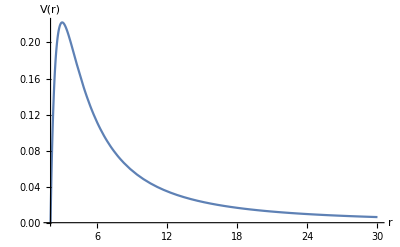

```mathematica
Plot[VtempEven, {r,2.001,30},AxesLabel->{"r","V(r)"},PlotRange->All]
```